```mathematica
TEM23
```

TEM23

X-Richtung:

X-Richtung:

{μ→421.674,σ→109.897,k→1162.62}

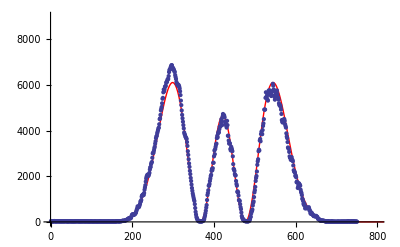

ⅇ^(-(2 (x-μ)^2)/σ^2) k (-2+(8 (x-μ)^2)/σ^2)^2

Y-Richtung:

{μ→248.956,σ→121.569,k→224.818}

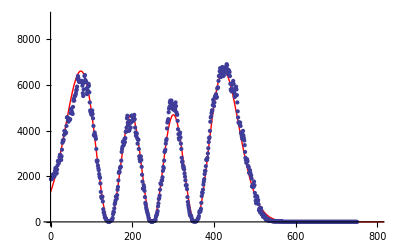

ⅇ^(-(2 (x-μ)^2)/σ^2) k ((16 √2 (x-μ)^3)/σ^3-(12 √2 (x-μ))/σ)^2

```mathematica
rawData = Import[NotebookDirectory[]<>"TEM23.dat"];
messData  = ToExpression[rawData];
xData = Map[First, messData];
yData = Map[Last, messData];

xKnoten = 2;
yKnoten = 3;

Clear @ model;
model[x_] = k *Exp[- 2((x-μ)/σ)^2]*HermiteH[n, Sqrt[2]*(x-μ)/σ]^2;Print["X-Richtung:"];

Print["X-Richtung:"];
param=FindFit[xData, model[x] /. {n->xKnoten}, {{μ, 400}, {σ, 65}, {k, 100000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->xKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[xData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]
model[x]/.{n->xKnoten}

Print["Y-Richtung:"];

param=FindFit[yData, model[x]/. {n->yKnoten}, {{μ, 300}, {σ, 150}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->yKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[yData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]
model[x]/.{n->yKnoten}
```

```mathematica
TEM33
```

TEM33

X-Richtung:

{μ→442.4,σ→111.366,k→68.7467}

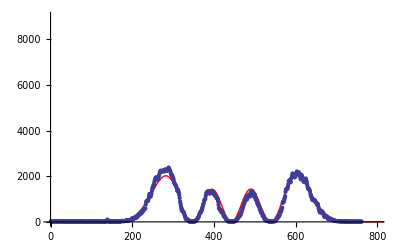

Y-Richtung:

{μ→244.328,σ→119.935,k→91.7463}

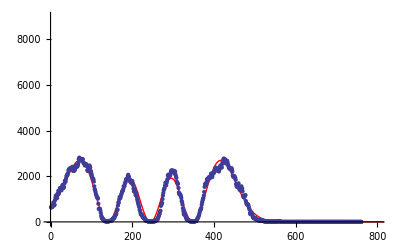

```mathematica
rawData = Import[NotebookDirectory[]<>"TEM33.dat"];
messData  = ToExpression[rawData];
xData = Map[First, messData];
yData = Map[Last, messData];

xKnoten = 3;
yKnoten = 3;

Clear @ model;
model[x_] = k *Exp[- 2((x-μ)/σ)^2]*HermiteH[n, Sqrt[2]*(x-μ)/σ]^2;Print["X-Richtung:"];

param=FindFit[xData, model[x] /. {n->xKnoten}, {{μ, 450}, {σ, 80}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->xKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[xData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]

Print["Y-Richtung:"];

param=FindFit[yData, model[x]/. {n->yKnoten}, {{μ, 200}, {σ, 100}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->yKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[yData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]
```

```mathematica
TEM50
```

TEM50

X-Richtung:

ⅇ^(-(2 (x-μ)^2)/σ^2) k ((128 √2 (x-μ)^5)/σ^5-(320 √2 (x-μ)^3)/σ^3+(120 √2 (x-μ))/σ)^2

{μ→440.895,σ→113.295,k→1.4719}

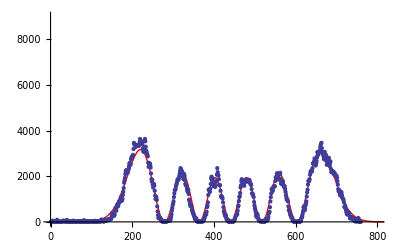

Y-Richtung:

{μ→231.669,σ→119.477,k→3597.15}

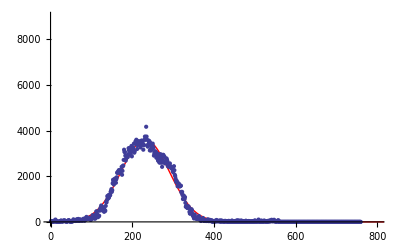

```mathematica
rawData = Import[NotebookDirectory[]<>"TEM50.dat"];
messData  = ToExpression[rawData];
xData = Map[First, messData];
yData = Map[Last, messData];

xKnoten = 5;
yKnoten = 0;

Clear @ model;
model[x_] = k *Exp[- 2((x-μ)/σ)^2]*HermiteH[n, Sqrt[2]*(x-μ)/σ]^2;Print["X-Richtung:"];
model[x] /.{n->xKnoten}

param=FindFit[xData, model[x] /. {n->xKnoten}, {{μ, 450}, {σ, 100}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->xKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[xData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]

Print["Y-Richtung:"];

param=FindFit[yData, model[x]/. {n->yKnoten}, {{μ, 300}, {σ, 100}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->yKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[yData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]
```

```mathematica
TEM52
```

TEM52

X-Richtung:

{μ→419.064,σ→106.67,k→444.784}

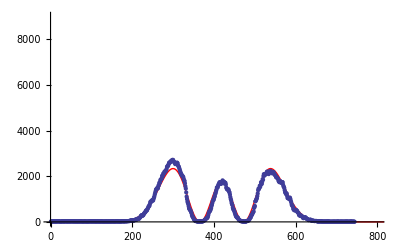

Y-Richtung:

{μ→252.043,σ→121.722,k→1.02425}

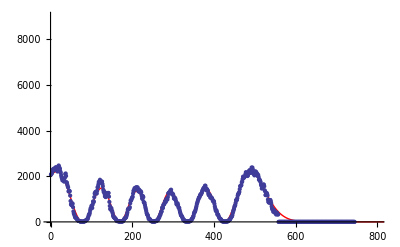

```mathematica
rawData = Import[NotebookDirectory[]<>"TEM25.dat"];
messData  = ToExpression[rawData];
xData = Map[First, messData];
yData = Map[Last, messData];

xKnoten = 2;
yKnoten = 5;

Clear @ model;
model[x_] = k *Exp[- 2((x-μ)/σ)^2]*HermiteH[n, Sqrt[2]*(x-μ)/σ]^2;Print["X-Richtung:"];

param=FindFit[xData, model[x] /. {n->xKnoten}, {{μ, 400}, {σ, 50}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->xKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[xData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]

Print["Y-Richtung:"];

param=FindFit[yData, model[x]/. {n->yKnoten}, {{μ, 250}, {σ, 100}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->yKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[yData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]
```